Liron, N., and R. Shahar. “Stokes flow due to a Stokeslet in a pipe.” Journal of Fluid Mechanics 86.4 (1978): 727-744.
Integrate uij (i, j = (R, theta, z)) about z and theta.

```mathematica
Clear["Global`*"]
$Assumptions=And@@Thread[{n}>0]&&Element[{ReF,ImF,an,bn,z,k,theta},Reals];
F=ReF+ImF*ⅈ;
(*theta=2*Pi/ph*z;*)
t1=Exp[-bn*z]*Im[ComplexExpand[Exp[ⅈ*an*z]*F]]*Cos[k*theta];
Integrate[t1,z]
Integrate[t1,theta]
Integrate[Integrate[t1,z],theta]
Integrate[Integrate[t1,theta],z]
FullSimplify[t1]
```

(ⅇ^(-bn z) Cos[k theta] (-(bn ImF+an ReF) Cos[an z]+(an ImF-bn ReF) Sin[an z]))/(an^2+bn^2)

(ⅇ^(-bn z) Sin[k theta] (ImF Cos[an z]+ReF Sin[an z]))/k

(ⅇ^(-bn z) Sin[k theta] (-(bn ImF+an ReF) Cos[an z]+(an ImF-bn ReF) Sin[an z]))/((an^2+bn^2) k)

(ⅇ^(-bn z) Sin[k theta] (-(bn ImF+an ReF) Cos[an z]+(an ImF-bn ReF) Sin[an z]))/((an^2+bn^2) k)

ⅇ^(-bn z) Cos[k theta] (ImF Cos[an z]+ReF Sin[an z])

Helical distribution of Stokeslets in pipe

```mathematica
Clear["Global`*"]
$Assumptions=And@@Thread[{an,bn,cn,k,ph}>0]&&Element[{ReF,ImF,an,bn,cn,ph,theta},Reals]&&Element[{k},Integers];
F=ReF+ImF*ⅈ;
z=ph/(2*Pi)*theta;
t1=FullSimplify[Exp[-bn*z]*Im[ComplexExpand[Exp[ⅈ*an*z]*F]]*Cos[k*theta]];
t1
FullSimplify[Integrate[t1,{theta,0,2*Pi}]]
```

ⅇ^(-(bn ph theta)/(2 π)) Cos[k theta] (ImF Cos[(an ph theta)/(2 π)]+ReF Sin[(an ph theta)/(2 π)])

(2 ⅇ^(-bn ph) ph π (ⅇ^(bn ph) (bn ImF ((an^2+bn^2) ph^2+4 k^2 π^2)+an ((an^2+bn^2) ph^2-4 k^2 π^2) ReF)-(bn ImF ((an^2+bn^2) ph^2+4 k^2 π^2)+an ((an^2+bn^2) ph^2-4 k^2 π^2) ReF) Cos[an ph]+(an ImF ((an^2+bn^2) ph^2-4 k^2 π^2)-bn ((an^2+bn^2) ph^2+4 k^2 π^2) ReF) Sin[an ph]))/((an^2+bn^2)^2 ph^4-8 (an-bn) (an+bn) k^2 ph^2 π^2+16 k^4 π^4)

Liron, N., and R. Shahar. “Stokes flow due to a Stokeslet in a pipe.” Journal of Fluid Mechanics 86.4 (1978): 727-744.
compute ringlet, Integrate uij (i, j = (R, theta, z)) about theta.

```mathematica
Clear["Global`*"];
$Assumptions=Element[{phi,tAFR1n,tAFPhi1n,tBFz1n,tAFR2n,tAFPhi2n,tBFz2n,tBFR3n,tBFPhi3n,tAFz3n},Reals]&&Element[{k},Integers];uR1n[k_,phi_]=tAFR1n*Cos[k*phi];
uPhi1n[k_,phi_]=tAFPhi1n*Sin[k*phi];
uz1n[k_,phi_]=tBFz1n*Cos[k*phi];
uR2n[k_,phi_]=tAFR2n*Sin[k*phi];
uPhi2n[k_,phi_]=tAFPhi2n*Cos[k*phi];
uz2n[k_,phi_]=tBFz2n*Sin[k*phi];
uR3n[k_,phi_]=tBFR3n*Cos[k*phi];
uPhi3n[k_,phi_]=tBFPhi3n*Sin[k*phi];
uz3n[k_,phi_]=tAFz3n*Cos[k*phi];
```

### part 1: k != 0, all components vanished.

```mathematica
Srr[k_,phi_]={{uR1n[k,phi],uR2n[k,phi],uR3n[k,phi]},
{uPhi1n[k,phi],uPhi2n[k,phi],uPhi3n[k,phi]},
{uz1n[k,phi],uz2n[k,phi],uz3n[k,phi]}};
MatrixForm[Srr[k,phi]];
Sxr[k_,phi_]=Simplify[Srr[k,phi]]
MatrixForm[Sxr[k,phi]]
IntSxr[k_,phi_]=Integrate[Sxr[k,phi],{phi,0,2*Pi}];
MatrixForm[IntSxr[k,phi]]
```

{{tAFR1n Cos[k phi],tAFR2n Sin[k phi],tBFR3n Cos[k phi]},{tAFPhi1n Sin[k phi],tAFPhi2n Cos[k phi],tBFPhi3n Sin[k phi]},{tBFz1n Cos[k phi],tBFz2n Sin[k phi],tAFz3n Cos[k phi]}}

(tAFR1n Cos[k phi] | tAFR2n Sin[k phi] | tBFR3n Cos[k phi]
tAFPhi1n Sin[k phi] | tAFPhi2n Cos[k phi] | tBFPhi3n Sin[k phi]
tBFz1n Cos[k phi] | tBFz2n Sin[k phi] | tAFz3n Cos[k phi])

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

### part 2: k == 0

```mathematica
IntSxr[phi_]=Integrate[Sxr[0,phi],{phi,0,2*Pi}];
MatrixForm[IntSxr[phi]]
```

(2 π tAFR1n | 0 | 2 π tBFR3n
0 | 2 π tAFPhi2n | 0
2 π tBFz1n | 0 | 2 π tAFz3n)

```mathematica
MatrixForm[IntSxr[k,phi]];
t1=IntSxr[k,phi][[3,3]];
pw=PageWidth/.Options[$Output];
SetOptions[$Output,PageWidth->Infinity];
MatrixForm[t1];
FortranForm[t1]
SetOptions[$Output,PageWidth->pw];
```

(AFz3n(xn,yn,k,z,b,R)*Sin(2*k*Pi))/k

```mathematica
FullSimplify[Integrate[Sxr[k,phi][[1,1]],{phi,0,2*Pi}]]
```

∫_0^(2 π) (Cos[phi] Cos[k phi] (t_AFR1nL+t_AFR1nR)+(t_AFPhi1nL+t_AFPhi1nR) Sin[phi] Sin[k phi])ⅆphi

```mathematica
FullSimplify[Integrate[ Sin[k*phi],phi]]
```

-Cos[k phi]/k

{{y→0},{y→0},{y→0},{y→0},{y→0},{y→0},{y→0},{y→0},{y→0},{y→0},{y→0},{y→0},{y→0},{y→0},{y→0},{y→0},{y→0},{y→0},{y→0},{y→0},{y→0},{y→0},{y→0},{y→0},{y→0},{y→0},{y→0},{y→0},{y→0}}

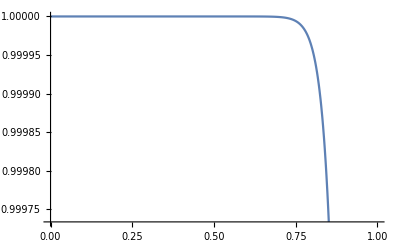

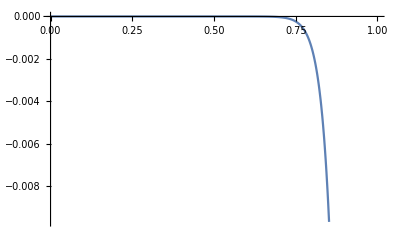

```mathematica
Clear["Global`*"];
a=1;
b=1;
n=30;
x=a*(1-(y/b)^n)^(1/n);
dx=FullSimplify[D[x,y]];
(*Solve[dx==0,y]*)
Plot[x,{y,0,a}]
Plot[dx,{y,0,a}]
```